# Test Values for Colloid Forces

Boltzmann constant in J/K.

```mathematica
kb=1.380649*10^-23;
```

Avogadro’s number.

```mathematica
avogadrosNumber=6.02214076*10^23;
```

Vacuum permittivity in J/(V^2 m).

```mathematica
ϵ0Si=8.8541878128*10^-12
```

8.85419×10^-12

Vacuum permittivity in J/(mV^2 nm).

```mathematica
ϵ0=ϵ0Si*1/((10^3)^2*10^9);
```

Conversion factor from J to kJ/mol.

```mathematica
convJTokJPerMole=avogadrosNumber/10^3;
```

Steric potential in kJ/mol.

```mathematica
repPot[h_,r1_,r2_,l_,σ_,t_]:=HeavisideTheta[2*l-h]*kb*t*(16*π*((r1+r2)/2)*l^2*σ^(3/2))/35*(28*(((2*l)/h)^(1/4)-1)+20/11*(1-(h/(2*l))^(11/4))+12*(h/(2*l)-1))*convJTokJPerMole;
```

Electrostatic potential in kJ/mol.

```mathematica
attPot[h_,r1_,r2_,psi1_,psi2_,ld_,ϵ_]:=2*π*ϵ*ϵ0*psi1*psi2*(2/(1/r1+1/r2))*Exp[-h/ld]*convJTokJPerMole;
```

Electrostatic potential with logarithm in kJ/mol.

```mathematica
attPotLog[h_,r1_,r2_,psi1_,psi2_,ld_,ϵ_]:=2*π*ϵ*ϵ0*psi1*psi2*(2/(1/r1+1/r2))*Log[1+Exp[-h/ld]]*convJTokJPerMole;
```

Test parameters.

```mathematica
r1=325;r2=65;psi1=50;psi2=-40;σ=0.09;l=10;ld=5;ϵ=80;t=298;
```

Test at h=10 (i.e., h=L).

```mathematica
NumberForm[repPot[10,r1,r2,l,σ,t]+attPot[10,r1,r2,psi1,psi2,ld,ϵ],16]
```

1505.829355134808

```mathematica
NumberForm[repPot[10,r1,r2,l,σ,t]+attPotLog[10,r1,r2,psi1,psi2,ld,ϵ],16]
```

1510.711567854979

Test at h=20 (i.e., h=2L).

```mathematica
NumberForm[repPot[20,r1,r2,l,σ,t]+attPot[20,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.63613061419315

```mathematica
NumberForm[repPot[20,r1,r2,l,σ,t]+attPotLog[20,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.53990009001303

Test slightly below h=20 (i.e., slightly below h=2L).

```mathematica
NumberForm[repPot[20-0.1,r1,r2,l,σ,t]+attPot[20-0.1,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.84996692702675

```mathematica
NumberForm[repPot[20-0.1,r1,r2,l,σ,t]+attPotLog[20-0.1,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.74983348860948

Test slightly above h=20 (i.e., slightly above h=2L).

```mathematica
NumberForm[repPot[20+0.1,r1,r2,l,σ,t]+attPot[20+0.1,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.42552111714948

```mathematica
NumberForm[repPot[20+0.1,r1,r2,l,σ,t]+attPotLog[20+0.1,r1,r2,psi1,psi2,ld,ϵ],16]
```

-10.33304182104529

Test at h=30 (i.e., h=3L).

```mathematica
NumberForm[repPot[30,r1,r2,l,σ,t]+attPot[30,r1,r2,psi1,psi2,ld,ϵ],16]
```

-1.439443749213437

```mathematica
NumberForm[repPot[30,r1,r2,l,σ,t]+attPotLog[30,r1,r2,psi1,psi2,ld,ϵ],16]
```

-1.437662679662967

Test at h=100 (i.e., h=20*ld).

```mathematica
NumberForm[repPot[100,r1,r2,l,σ,t]+attPot[100,r1,r2,psi1,psi2,ld,ϵ],16]
```

-1.196938817005087×10^-6

```mathematica
NumberForm[repPot[100,r1,r2,l,σ,t]+attPotLog[100,r1,r2,psi1,psi2,ld,ϵ],16]
```

-1.196938856264202×10^-6

Test system of four particles.

```mathematica
NumberForm[
repPot[30,r1,r1,l,σ,t]+attPot[30,r1,r1,psi1,psi1,ld,ϵ]
+ repPot[20, r1, r2, l, σ,t]+attPot[20,r1,r2,psi1,psi2,ld,ϵ]
+repPot[10,r1,r2,l,σ,t]+attPot[10,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{2*r1+30,0,0}-{0,r1+r2+20,0}]-r1-r2,r1,r2,l,σ,t]+attPot[Norm[{2*r1+30,0,0}-{0,r1+r2+20,0}]-r1-r2,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{2*r1+30,0,0}-{0,0,r1+r2+10}]-r1-r2,r1,r2,l,σ,t]+attPot[Norm[{2*r1+30,0,0}-{0,0,r1+r2+10}]-r1-r2,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{0,r1+r2+20,0}-{0,0,r1+r2+10}]-r2-r2,r2,r2,l,σ,t]+attPot[Norm[{0,r1+r2+20,0}-{0,0,r1+r2+10}]-r2-r2,r2,r2,psi2,psi2,ld,ϵ]
,16]
```

1500.591138580165

```mathematica
NumberForm[
repPot[30,r1,r1,l,σ,t]+attPotLog[30,r1,r1,psi1,psi1,ld,ϵ]
+ repPot[20, r1, r2, l, σ,t]+attPotLog[20,r1,r2,psi1,psi2,ld,ϵ]
+repPot[10,r1,r2,l,σ,t]+attPotLog[10,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{2*r1+30,0,0}-{0,r1+r2+20,0}]-r1-r2,r1,r2,l,σ,t]+attPotLog[Norm[{2*r1+30,0,0}-{0,r1+r2+20,0}]-r1-r2,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{2*r1+30,0,0}-{0,0,r1+r2+10}]-r1-r2,r1,r2,l,σ,t]+attPotLog[Norm[{2*r1+30,0,0}-{0,0,r1+r2+10}]-r1-r2,r1,r2,psi1,psi2,ld,ϵ]
+repPot[Norm[{0,r1+r2+20,0}-{0,0,r1+r2+10}]-r2-r2,r2,r2,l,σ,t]+attPotLog[Norm[{0,r1+r2+20,0}-{0,0,r1+r2+10}]-r2-r2,r2,r2,psi2,psi2,ld,ϵ]
,16]
```

1505.562902813702

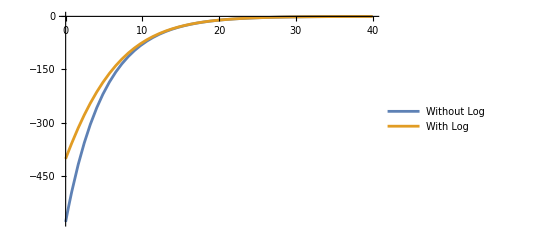

```mathematica
Plot[{attPot[h,r1,r2,psi1,psi2,ld,ϵ],attPotLog[h,r1,r2,psi1,psi2,ld,ϵ]},{h,0,40},PlotLegends->{"Without Log", "With Log"},PlotRange->All]
```